```mathematica
Begin["BoatContext`"];
libboatLocation="/home/wolf/qea/libboat.nb";
libboat=NotebookOpen[libboatLocation];
SelectionMove[libboat,All,Notebook];
SelectionEvaluate[libboat];
Needs["CUDALink`"];
```

```mathematica
bHullFileLocation="/home/wolf/qea/bhull.stl";
hullFileLocation="/home/wolf/qea/hull.stl";

bHullFileLocation="/home/wolf/qea/hulls/boats/boatboatfixed.stl";
hullFileLocation="/home/wolf/qea/hulls/boats/boatboatfixed.stl";

canFileLocation="/home/wolf/qea/can.stl";
can=Import[canFileLocation,"BoundaryMeshRegion"];

mastFileLocation="/home/wolf/qea/mast.stl";
mast=Import[mastFileLocation,"BoundaryMeshRegion"];

(* Convert from STL file units to cm *)
stlUnits="Meters";
stlScale=QuantityMagnitude[UnitConvert[stlUnits,Quantity[, "Centimeters"]]];

(* Generate point cloud *)
buoyHullNonScaled=Import[bHullFileLocation,"BoundaryMeshRegion"];
buoyHull=TransformedRegion[buoyHullNonScaled,ScalingTransform[{stlScale,stlScale,stlScale}]];
(*buoyHull=Import["/home/wolf/qea/hulls/cube/cube.stl","BoundaryMeshRegion"];*)
buoyHullVolume=Volume[buoyHull]Quantity[, ("Centimeters")^3];
buoyHullPoints=pointCloud[buoyHull,100000];

hullNonScaled=Import[hullFileLocation,"BoundaryMeshRegion"];
hull=TransformedRegion[hullNonScaled,ScalingTransform[{stlScale,stlScale,stlScale}]];
(*hull=Import["/home/wolf/qea/hulls/cube/cube.stl","BoundaryMeshRegion"];*)
hullVolume=Volume[buoyHull]Quantity[, ("Centimeters")^3];
hullCentroid=RegionCentroid[hull];

(* Constants *)
(*GeogravityModelData[CityData[Entity["City",{"Needham","Massachusetts","UnitedStates"}],"Coordinates"],"Magnitude"];*)
g=9.81 Quantity[, ("Meters")/("Seconds")^2];
blueFoamDensity=0.0317 Quantity[, ("Grams")/("Centimeters")^3];
waterDensity=1 Quantity[, ("Grams")/("Centimeters")^3];
```

```mathematica
can1Loc={0,4.5-2,9.35};
can2Loc={0,4.5-2,26};

canLocs=canLocationFinder[hullCentroid,8,-4];
can1Loc=canLocs[[1]];
can2Loc=canLocs[[2]];

mastLoc=mastLocationFinder[hullCentroid,25-2];

frontVec=Normalize[{1,0,0}];
boat={
<|
name->"BuoyHull",
type->"Buoy",
mass->buoyHullVolume*waterDensity,
volume->buoyHullVolume,
points->buoyHullPoints,
region->bouyHull,
render->{GraphicsComplex[MeshCoordinates@buoyHull,MeshCells[buoyHull,2]]},
cobRender->({White,PointSize[Large],Point[#]}&)
|>,
<|
name->"Hull",
type->"PointMass",
mass->hullVolume*blueFoamDensity,
volume->hullVolume,
com->Quantity[hullCentroid,"Centimeters"],
render->{
{Black,PointSize[Large],Point[hullCentroid]},
{EdgeForm[],Opacity[.6],LightPink,GraphicsComplex[MeshCoordinates@hull,MeshCells[hull,2]]}
}
|>,
<|
name->"Can",
type->"PointMass",
mass->389.5 Quantity[, "Grams"],
com->Quantity[can1Loc,"Centimeters"],
render->{
{Black,PointSize[Large],Point[can1Loc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@can,MeshCells[can,2]],can1Loc]}
}
|>,
<|
name->"Can",
type->"PointMass",
mass->389.5 Quantity[, "Grams"],
com->Quantity[can2Loc,"Centimeters"],
render->{
{Black,PointSize[Large],Point[can2Loc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@can,MeshCells[can,2]],can2Loc]}
}
|>,
<|
name->"Mast",
type->"PointMass",
mass->96.2 Quantity[, "Grams"],
com->Quantity[mastLoc,"Centimeters"],
render->{
{Black,PointSize[Large],Point[mastLoc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@mast,MeshCells[mast,2]],mastLoc]}
}
|>
};
Show[renderBoatWithForces[boat,Normalize[{0,0,1}]],ViewPoint->{0,-∞,0}]
```

-Graphics3D-

## Boats

```mathematica
renderBoatWithForces[boat,Normalize[{0,0,1}]]
```

-Graphics3D-

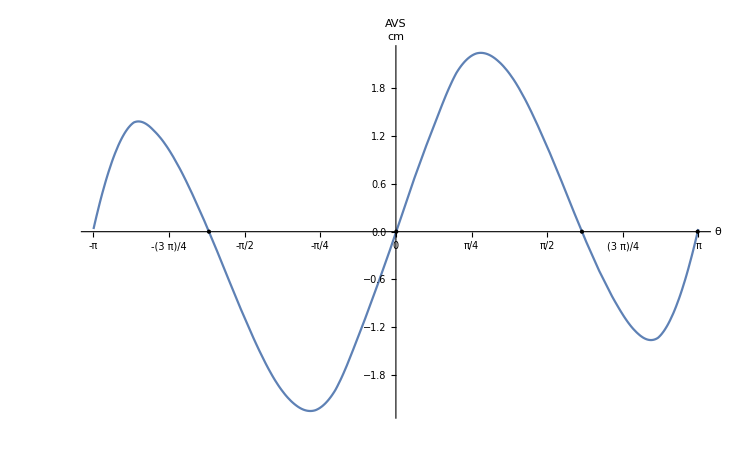

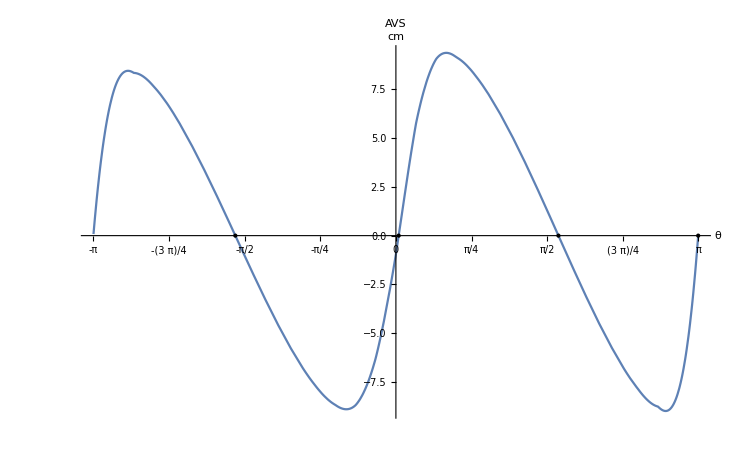

```mathematica
DistributeDefinitions["BoatContext`"];
plotCircleAVS[boat,30,FrontVec->{1,0,0}]
plotCircleAVS[boat,30,FrontVec->{0,1,0}]
```

```mathematica
manyBoats[boat,10,FrontVec->{0,1,0},ViewPoint->{0,∞,0}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

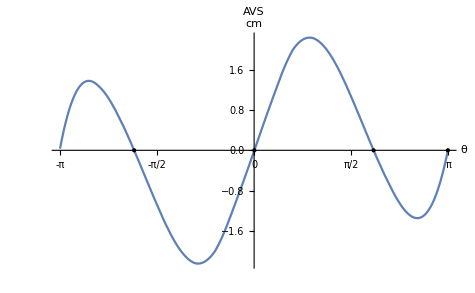
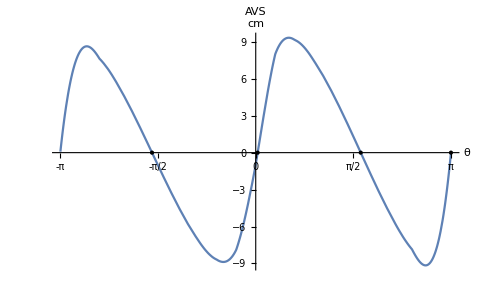
get Boat | -Graphics3D-
AVS Plot | -Graphics-
AVS Zeros | -111.237 ° | 8.92888 ° | 110.774 ° | 179.263 °
Trim AVS | -Graphics-
Trim | 1.78611

```mathematica
boatSummary[boat]
```